## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

## Equation and and Eigenvalue function

```mathematica
Eq=EqTeukolskyRadial/.RuleKRadial;
```

```mathematica
Clear@ℰ;
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative]:=ℰ[𝓈,ℓ,-𝓂,-𝒸];
ℰ[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[-𝓈,ℓ,𝓂,𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]/;ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=SpinWeightedSpheroidalHarmonicEigenvalue[𝓈,ℓ,𝓂,N@𝒸];
(*ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]/;ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=(Simplify[SWSHEigenCoef//.Rule𝒽∪Ruleκpm∪{s->𝓈,m->𝓂}]/.l->ℓ).Table[𝒸^(i-1),{i,Length@SWSHEigenCoef}];*)
```

## Parameter rules and equation simplification

```mathematica
RuleRHorizon={R->Function[x,x^(-s-I χ/τ)f[x]]};
EquationF=PowerExpand@Simplify[x^(s+I χ/τ)x (x+τ) (Eq/.RuleRHorizon)];
(* all params *)
RuleBoundaryBH={𝒶[0]->1,𝒷[0]->(-ℬ τ^2)/(4 (ⅈ τ/2+χ) χ)};
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+(s+1)s)^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+ℰ[s,l,m,(𝒥 ω̄)/rp]-s(s+1)};
```

```mathematica
(* Function to replace all parameters accordingly *)
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_]=#1//.RuleBoundaryBH∪RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}&;
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_,𝓌_]=#1//.RuleBoundaryBH∪RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}&;
```

```mathematica
(* Coeficients to estimate f and f' close to BH horizon *)
nCoefH=6;
RuleFHorizon={f->Function[x,∑_(n=0)^nCoefH 𝒶[n] x^n]};
FSeriesCoefHorizon=First@Solve[CoefficientList[EquationF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
```

```mathematica
(* Coeficients to estimate Ain and Aout at infinity *)
nCoefInf=10;
RuleRinInf={R->Function[x,ⅇ^(-ⅈ ω̄ x)x^(-1-ⅈ ω̄ (2-τ)) ∑_(n=0)^nCoefInf 𝒾[n] x^-n]};
RuleRoutInf={R->Function[x,ⅇ^(ⅈ ω̄ x) x^(-1-2 s+ⅈ ω̄ (2-τ)) ∑_(n=0)^nCoefInf ℴ[n] x^-n]};
```

## Equation solver definition

```mathematica
(* OptionsPattern to use with SolveωF to get more precision/accuracy out of NDSolve *)
IncreasePrecision={PrecisionGoal->10,AccuracyGoal->12,MaxSteps->10^8};
```

#### Solver 1

```mathematica
(* Definition of the solver for s=1 and s=-1 equations using boundary conditions at BH horizon *)
Clear[SolveSingle];
SolveSingle[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,{omega__?NumberQ},opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{eqF,delω,incs,fINF,k=0,last,olist,localk},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-14.;
xINF:=2 π/Abs[ω̄]*750.;

(* stuff to monitor asynchronously SolveωF using ParallelTable *)
SetSharedVariable[k];
ParallelEvaluate[last=AbsoluteTime[];localk=1];

(* using ReplaceParams once to save computation time *)
{eqF,delω,incs,fINF}=ReplaceParams[𝒿,𝓈,ℓ,𝓂][{EquationF,m Ω̄,({f[x0],f'[x0]}/.RuleFHorizon/.FSeriesCoefHorizon),f[xINF] ⅇ^(ⅈ(Sign[𝓈] ω̄ (xINF+(2-τ)Log[xINF])-χ/τ Log[xINF]))}];
olist=DeleteCases[{omega},(delω|0.|0)];
(* use Monitor ProgressIndicator with asynchronous refresh of the calculation state *)
Monitor[ParallelTable[
(* calculation state update with suppressed output *)
localk++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];k+=localk;localk=0];

(* solving the equation using NDSolve and substituing the result *)
{𝒿,ω̄,fINF}/.First@NDSolve[{eqF==0,{f[x0],f'[x0]}==incs},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]],{ω̄,olist}],
ProgressIndicator[k,{0,Length@olist}]]
];
```

#### Solver 2

```mathematica
Clear[SolveBoth];
SolveBoth[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝓌_?NumberQ,opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{eqF,f0,fp0,coefInInf,coefOutInf,in,out,ev,x0,xINF},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF=2Pi/Abs[𝓌]*80.;
ev=ℰ[𝓈,ℓ,𝓂,(𝒿 𝓌)/(1+Sqrt[1-𝒿^2])];
eqF=EquationF//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌];

{f0,fp0}={f[x0],f'[x0]}/.RuleFHorizon/.First@Solve[CoefficientList[eqF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
coefInInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(ⅈ ω̄ x) x^(ⅈ ω̄ (2-τ)) Eq/.RuleRinInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[𝒾[n],{n,1,nCoefInf}]];
coefOutInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(-ⅈ ω̄ x) x^(2 s-ⅈ ω̄ (2-τ)) Eq/.RuleRoutInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[ℴ[n],{n,1,nCoefInf}]];
{in,out}=Total@ReplaceParams[𝒿,𝓈,l,𝓂,𝓌][{R[x]/.RuleRinInf/.coefInInf,R[x]/.RuleRoutInf/.coefOutInf}]//{𝒾[0],ℴ[0]}/.First@Solve[{#==RInf,D[#,x]==RpInf}/.{x->xINF,ℰ[__]->ev},{𝒾[0],ℴ[0]}]&;
 
{𝒿,𝓌,in,out}/.ReplaceParams[𝒿,𝓈,l,𝓂,𝓌][{RInf->R[xINF],RpInf->R'[xINF]}/.RuleRHorizon]/.First@NDSolve[{eqF==0,f0==f[x0],fp0==f'[x0]}/.{ℰ[__]->ev,𝒶[0]->1},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]]
];
```

## Analysis

```mathematica
rng=Range[0.01,0.99,0.04]∪{0.98,0.99,0.999,0.9999};
```

```mathematica
test1=ParallelTable[ReplaceParams[𝒿,-1,40,1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,1,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{𝒿,rng}];
```

```mathematica
test2=ParallelTable[ReplaceParams[𝒿,-1,40,0,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,0,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{𝒿,rng}];
```

```mathematica
test3=ParallelTable[ReplaceParams[𝒿,-1,40,-1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,-1,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{𝒿,rng}];
```

```mathematica
test4=ParallelTable[ReplaceParams[𝒿,-1,30,7,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,30,7,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{𝒿,rng}];
```

FittedModel[-2.72831-(3.50601 x^2)/((1+√(1-x^2))^2)]

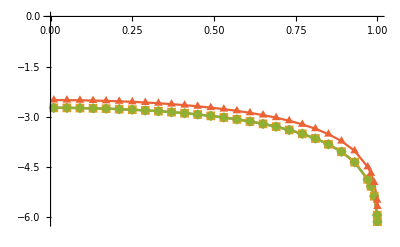

```mathematica
data1={rng[[#]],((Arg@test1[[#,3]]+If[Arg@test1[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data2={rng[[#]],((Arg@test2[[#,3]]+If[Arg@test2[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data3={rng[[#]],((Arg@test3[[#,3]]+If[Arg@test3[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data4={rng[[#]],((Arg@test4[[#,3]]+If[Arg@test4[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
nlmf=NonlinearModelFit[data1,α+(β x^2)/(4(1+√(1-x^2))^2),{α,β,γ},x]
dataA={#,nlmf[#]}&/@rng;
{data1,data2,data3,data4}//ListPlot[#,Joined->True,PlotRange->All,PlotMarkers->Automatic]&
```

```mathematica
1/Sqrt[1-0.99^2]
```

7.08881

```mathematica
modes2=ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.99,-1,ℓ,𝓂,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{ℓ,1,40},{𝓂,1,1}]//Flatten[#,1]&;
```

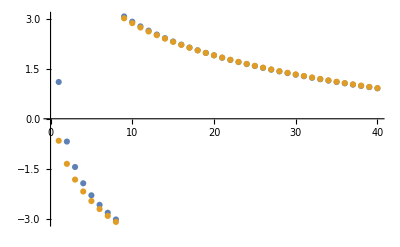

```mathematica
{{#1,Arg@#3}&@@@modes2,{#,Arg[Gamma[#+1-1.81003*I 0.4]/Gamma[#+1+1.81003*I  0.4]]}&@@@modes2}//ListPlot
```

```mathematica
NonlinearModelFit[{#1,Arg@#3}&@@@modes2[[9;;]],Arg[Gamma[x+1-β I 0.4]/Gamma[x+1+β I 0.4]],{{β,1.81}},x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
β | 1.81003 | 0.00117242 | 1543.84 | 2.64283×10^-77

```mathematica
values2=Table[#,{θ,0.,Pi,Pi/300.}]&/@ParallelTable[(modes2⟦ℓ,3⟧-Gamma[ℓ+1-1.81003*I 0.4]/Gamma[ℓ+1+1.81003*I 0.4])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,modes2⟦All,1⟧}];
```

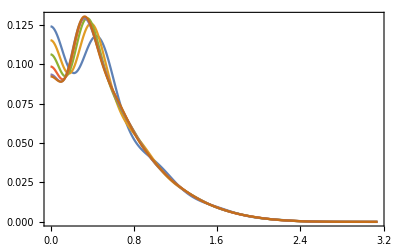

```mathematica
{Range[0,Pi,Pi/300],Abs[Total@values2[[1;;#]]]^2}ᵀ&/@{10,12,14,16,18,20}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01]]&
```

```mathematica
Plot[{(#3-Gamma[#1+1-1.81I 0.4]/Gamma[#1+1+1.81I 0.4])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,#1,#2,0,0]*SpinWeightedSphericalHarmonicY[-1,#1,#2,θ,0]&@@@Flatten[modes2⟦Range[21]⟧,1]//ComplexExpand[Abs[Total@#]^2]&,(#3-Gamma[#1+1-1.81I 0.4]/Gamma[#1+1+1.81I 0.4])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,#1,#2,0,0]*SpinWeightedSphericalHarmonicY[-1,#1,#2,θ,0]&@@@Flatten[modes2⟦Range[14]⟧,1]//ComplexExpand[Abs[Total@#]^2]&,(#3-Gamma[#1+1-1.81I 0.4]/Gamma[#1+1+1.81I 0.4])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,#1,#2,0,0]*SpinWeightedSphericalHarmonicY[-1,#1,#2,θ,0]&@@@Flatten[modes2⟦Range[7]⟧,1]//ComplexExpand[Abs[Total@#]^2]&}//Evaluate,{θ,0,π},PlotRange->All]
```

$Aborted

## Export data

```mathematica
Clear[FormatZ,Formatϕ]
FormatZ[ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2 Abs[𝒶[0]]^2)/(χ Abs[#3]^2),-1/(1+(ℬ^2 τ^2 Abs[#4]^2)/(4 χ ω̄(τ^2+ 4 χ^2)Abs[𝒶[0]]^2)),(ℬ^2 τ^4)/(4 χ^2 (τ^2+4 χ^2))Abs[#4/#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
Formatϕ[ℓ_,𝓂_]:={#1,#2,Re[#3],Im[#3],Re[#4],Im[#4]}&;
```

```mathematica
Spin=Range[0.01,0.99,0.01]∪{0.995,0.999,0.9995,0.9999};
```

```mathematica
Omega=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[0,est,Round[est/450,0.0005]]]];
OmegaSpread=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[0,est,Round[est/100,0.0005]]]];
OmegaNegativeSpread=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[-est,est,Round[est/200,0.0005]]]];
OmegaDetailed=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},Range[0,First@TakeSmallest[{𝒿,est},1],First@TakeSmallest[{Ceiling[0.01𝒿,0.0001],Round[est/450,0.0005]},1]]]];
```

```mathematica
Table[ExportAllCSV[0.99,1,ℓ,𝓂,{0.3991}&,"precision2",{PrecisionGoal->12,AccuracyGoal->14,WorkingPrecision->MachinePrecision,MaxSteps->Automatic}],{ℓ,1,4},{𝓂,0,ℓ}];
```

Completed precision2 file with (𝓈,ℓ,m)=(1,1,0) for 1 spin(s) in 0h 05m 57s

Completed precision2 file with (𝓈,ℓ,m)=(1,1,1) for 1 spin(s) in 0h 06m 20s

Completed precision2 file with (𝓈,ℓ,m)=(1,2,0) for 1 spin(s) in 0h 05m 15s

Completed precision2 file with (𝓈,ℓ,m)=(1,2,1) for 1 spin(s) in 0h 05m 19s

Completed precision2 file with (𝓈,ℓ,m)=(1,2,2) for 1 spin(s) in 0h 05m 09s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,0) for 1 spin(s) in 0h 05m 28s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,1) for 1 spin(s) in 0h 05m 35s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,2) for 1 spin(s) in 0h 05m 42s

Completed precision2 file with (𝓈,ℓ,m)=(1,3,3) for 1 spin(s) in 0h 05m 27s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,0) for 1 spin(s) in 0h 05m 35s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,1) for 1 spin(s) in 0h 05m 41s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,2) for 1 spin(s) in 0h 05m 36s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,3) for 1 spin(s) in 0h 05m 28s

Completed precision2 file with (𝓈,ℓ,m)=(1,4,4) for 1 spin(s) in 0h 05m 22s

```mathematica
(*ExportAllCSV[0.99,1,1,1,Omega,"test2"]*)
```

```mathematica
(*ExportAllCSV[1,1,1,{0.995,0.999,0.9995,0.9999},Omega,"precision",IncreasePrecision]*)
```

```mathematica
Table[{#3,#5}&@@First@Import@GetZFile[1,ℓ,𝓂,"precision2"],{ℓ,1,4},{𝓂,0,ℓ}]//Column
```

{{-0.943775,-0.943892},{0.0328502,0.0328977}}
{{-0.00153209,-0.00149008},{5.78312×10^-7,0.0000424256},{0.000289971,0.000331642}}
{{-6.12064×10^-8,0.0000418814},{8.11492×10^-12,0.0000418156},{3.25204×10^-8,0.0000417071},{1.41635×10^-6,0.000042993}}
{{-1.12102×10^-12,0.0000421803},{7.07349×10^-17,0.0000417113},{1.49998×10^-12,0.0000417844},{1.87203×10^-10,0.0000416758},{4.30024×10^-9,0.0000417874}}

```mathematica
Table[Divide@@N[{#6^2+#5^2-#3^2-#4^2,#3^2+#4^2},20]&@@First@Import@GetϕFile[1,ℓ,𝓂,"precision2"],{ℓ,1,4},{𝓂,0,ℓ}]
```

{{-0.943892,0.0328977},{-0.00149008,0.0000424256,0.000331642},{0.0000418814,0.0000418156,0.0000417071,0.000042993},{0.0000421803,0.0000417113,0.0000417844,0.0000416758,0.0000417874}}

## Calculate In/Out flux

```mathematica
Mollweide:=Graphics[#/.{ϕ_Real,θ_Real}:>{2/Pi(ϕ-Pi)Sin[θ],Cos[θ]},ImageSize->Medium]&
```

```mathematica
Clear[OutFromInPackets,Ein,Eout]
OutFromInPackets[InConfig_?ArrayQ]:=Block[{ParsedPackets,YZCoefs,RatiosFromPackets,OutWavePackets},
ParsedPackets=(FlattenAt[#,{{1,2,3}}ᵀ]&)@*Map[DeleteDuplicates]@*Transpose/@GroupBy[InConfig,(Take[#1,3]&)->(Drop[#1,-1]&)];
YZCoefs=First/@GroupBy[
KeyValueMap[Sequence@@Thread@Join[#1,#2ᵀ]&,{Last@{##},Last/@SolveωF[#1,1,##2,IncreasePrecision],Last/@SolveωF[#1,-1,##2,IncreasePrecision]}ᵀ&@@@ParsedPackets],
(Take[#,4]&)->(Drop[#,4]&)];
RatiosFromPackets=(#2/#1&)@@@YZCoefs;
OutWavePackets=Most[#]~Join~{RatiosFromPackets[Take[#,4]]Last[#]}&/@InConfig
];
Ein[packets_?ArrayQ]:=ComplexExpand[ParallelSum[With[{j1=u⟦1⟧,l1=u⟦2⟧,m1=u⟦3⟧,ω1=u⟦4⟧,Y1=u⟦5⟧,j2=v⟦1⟧,l2=v⟦2⟧,m2=v⟦3⟧,ω2=v⟦4⟧,Y2=v⟦5⟧},Exp[I(ω2-ω1)t]Y2*Y1 SpinWeightedSphericalHarmonicY[1,l2,m2,θ,ϕ]*SpinWeightedSphericalHarmonicY[1,l1,m1,θ,ϕ]],{u,packets},{v,packets}],{ϵR,ϵL,ϵ1,ϵ2}]/.{f_[a_.+b_.t]->0};
Eout[packets_?ArrayQ]:=ComplexExpand[ParallelSum[With[{j1=u⟦1⟧,l1=u⟦2⟧,m1=u⟦3⟧,ω1=u⟦4⟧,Z1=u⟦5⟧,j2=v⟦1⟧,l2=v⟦2⟧,m2=v⟦3⟧,ω2=v⟦4⟧,Z2=v⟦5⟧},Exp[I(ω2-ω1)t]Z2*Z1 SpinWeightedSphericalHarmonicY[-1,l2,m2,θ,ϕ]*SpinWeightedSphericalHarmonicY[-1,l1,m1,θ,ϕ]],{u,packets},{v,packets}],{ϵR,ϵL,ϵ1,ϵ2}]/.{f_[a_.+b_.t]->0};
```

```mathematica
PolarizationRule[s_]=ComplexExpand@{ϵR->ϵ1-I ϵ2,ϵL->ϵ1+I ϵ2,ϵ1->Exp[I ϕ0]Cos[Pi-θ0],ϵ2->-Sign[s]I Exp[I ϕ0]};
```

```mathematica
(* testing configs *)
InTest=<|1->{{0.99,1,1,0.45,1}},
2->{{0.99,1,1,0.45,1},{0.99,1,-1,0.45,ϵ}},
3->{{0.99,1,-1,0.45,1},{0.99,1,1,0.45,ϵ}},
4->{{0.99,1,1,0.45,1},{0.99,1,1,-0.45,ϵ}},
5->{{0.99,1,1,-0.45,1},{0.99,1,1,0.45,ϵ}}
|>;
(* plane wave configs *)
InPlaneWave1=ParallelTable[{
{0.99,l,m,ω̄,4 Pi ϵR(-1)^(l+1)/(2 ω̄)SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*},
{0.99,l,m,-ω̄,4 Pi ϵL*(-1)^(l+1)/(-2 ω̄)SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*}
},{l,{1}},{m,-l,l},{ω̄,{0.45}}
]//Simplify[Flatten[Flatten[#,2],1],{θ0∈Reals,ϕ0∈Reals}]&;
InPlaneWave2=ParallelTable[{
{0.99,l,m,ω̄,(4 Pi ϵR)/(2 ω̄)(-1)^(l+1)SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*},
{0.99,l,m,-ω̄,(4 Pi ϵL*)/(2 ω̄)(-1)^l SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*}
},{l,{2}},{m,-l,l},{ω̄,{0.45}}
]//Simplify[Flatten[Flatten[#,2],1],{θ0∈Reals,ϕ0∈Reals}]&;
InPlaneWave3=ParallelTable[{
{0.99,l,m,ω̄,(4 Pi ϵR)/(2 ω̄)(-1)^(l+1)SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*},
{0.99,l,m,-ω̄,(4 Pi ϵL*)/(2 ω̄)(-1)^l SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*}
},{l,{3}},{m,-l,l},{ω̄,{0.45}}
]//Simplify[Flatten[Flatten[#,2],1],{θ0∈Reals,ϕ0∈Reals}]&;
InPlaneWave4=ParallelTable[{
{0.99,l,m,ω̄,(4 Pi ϵR)/(2 ω̄)(-1)^(l+1)SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*},
{0.99,l,m,-ω̄,(4 Pi ϵL*)/(2 ω̄)(-1)^l SpinWeightedSphericalHarmonicY[-1,l,m,θ0,ϕ0]*}
},{l,{4}},{m,-l,l},{ω̄,{0.45}}
]//Simplify[Flatten[Flatten[#,2],1],{θ0∈Reals,ϕ0∈Reals}]&;
```

```mathematica
OutPlaneWave1=OutFromInPackets[InPlaneWave1]//Chop;
```

```mathematica
OutPlaneWave2=OutFromInPackets[InPlaneWave2]//Chop;
```

```mathematica
OutPlaneWave3=OutFromInPackets[InPlaneWave3]//Chop;
```

```mathematica
OutPlaneWave4=OutFromInPackets[InPlaneWave4]//Chop;
```

```mathematica
With[{f=Chop@Eout[InPlaneWave0]//.PolarizationRule[1],g=0},
Manipulate[{fgBound=(First@Maximize[Chop@#,{θ,ϕ}]&/@{f,g})//Max;
Mollweide@@ContourPlot[f,{ϕ,0,2Pi},{θ,0,Pi},ImageSize->Medium,ColorFunction->(ColorData["TemperatureMap"][#/fgBound]&),ColorFunctionScaling->False,Frame->False,PlotRangePadding->None,Contours->30,AspectRatio->1,PlotRange->{0,fgBound}],Mollweide@@ContourPlot[g,{ϕ,0,2Pi},{θ,0,Pi},ImageSize->Medium,ColorFunction->(ColorData["TemperatureMap"][#/fgBound]&),ColorFunctionScaling->False,Frame->False,PlotRangePadding->None,Contours->30,AspectRatio->1,PlotRange->{0,fgBound}],
BarLegend[{"TemperatureMap",{0,fgBound}},30]}
,{θ0,0,Pi},{ϕ0,0,2Pi},{ϵ,0.0001,1}]
]
```

```mathematica
directions={0,Pi/6,Pi/4,Pi/3,Pi/2,Pi};
colors=ColorData["Rainbow"]/@Range[0,1,1/(Length@directions-1)];
(*{Plot[Ein/.({ϕ0->0,θ->#,ϕ->0}&/@directions)//Evaluate,{θ0,0,6π},ImageSize->Medium,PlotStyle->colors,FrameTicks->{Automatic,{Range[0,6Pi,Pi/2],None}},Frame->True,PlotRange->All],Plot[Eout/.({ϕ0->0,θ->#,ϕ->0}&/@directions)//Evaluate,{θ0,0,6π},ImageSize->Medium,PlotStyle->colors,FrameTicks->{Automatic,{Range[0,6Pi,Pi/2],None}},Frame->True,PlotRange->All],
LineLegend[colors,Row[{Subscript[θ, 0],"=",#}," "]&/@directions,LegendFunction->Panel,LegendLayout->"Row"]}//GraphicsRow*)
```

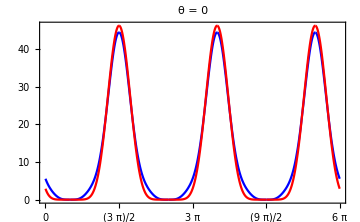
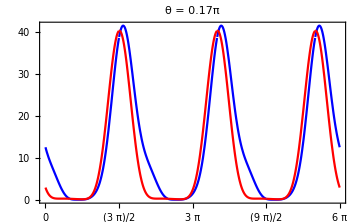
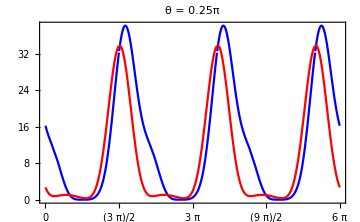
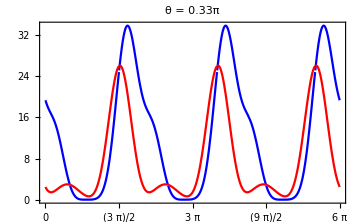
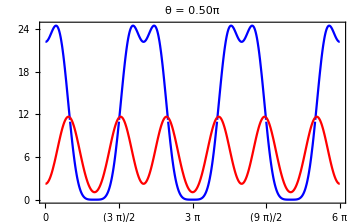
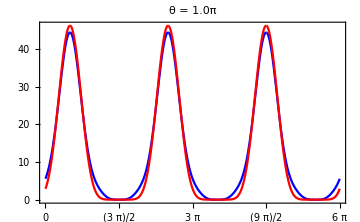

```mathematica
orbit[t_,γ_,x_]={ϕ0->ArcTan[Cos[t],Cos[γ] Sin[t]],θ->x,ϕ->0,θ0->Pi-ArcCos[Sin[γ]Sin[t]]};
Plot[{Eout[Join[InPlaneWave1]]//.PolarizationRule[1],Eout[Join[OutPlaneWave1]]//.PolarizationRule[1]}/.orbit[t,π/2,#]//Evaluate,{t,0,6π},PlotLabel->Row[{θ," = ",If[!PossibleZeroQ[#],ToString@N[#/Pi,2]<>"π",0]}],ImageSize->Medium,PlotStyle->{Blue,Red,Green},FrameTicks->{Automatic,{Range[0,6Pi,Pi/2],None}},Frame->True,PlotRange->All]&/@directions
```